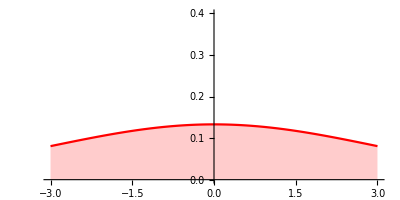

```mathematica
priordist=Plot[PDF[NormalDistribution[0,3],x],{x,-3,3},Filling->Axis, AxesOrigin->{0,0},PlotRange->{0,0.4},PlotStyle->Red, AspectRatio->1/2]
```

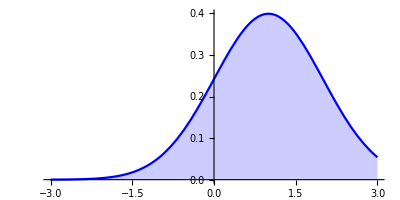

```mathematica
pdist=Plot[PDF[NormalDistribution[1,1],x],{x,-3,3},Filling->Axis, AxesOrigin->{0,0},PlotRange->{0,0.4},PlotStyle->Blue, AspectRatio->1/2]
```

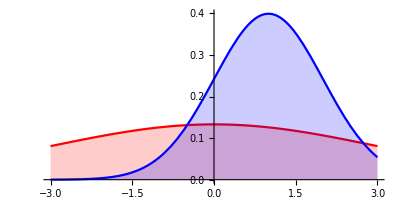

```mathematica
Show[priordist,pdist]
```

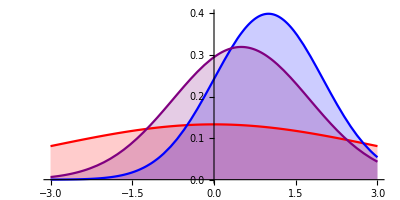

```mathematica
Plot[{PDF[NormalDistribution[1,1],x],PDF[NormalDistribution[0.5,1.25],x]},{x,-3,3},Filling->Axis, AxesOrigin->{0,0},PlotRange->{0,0.4},PlotStyle->{Blue,Purple}, AspectRatio->1/2]
```

```mathematica
pri = Plot[PDF[NormalDistribution[0,3],x],{x,-3,3},Filling->Axis, AxesOrigin->{0,0},PlotRange->{0,0.4},PlotStyle->Red, AspectRatio->1/2];
```

```mathematica
priordata=RandomVariate[NormalDistribution[0,3],200];
```

```mathematica
priorrange=Range[-3,3,0.25];
```

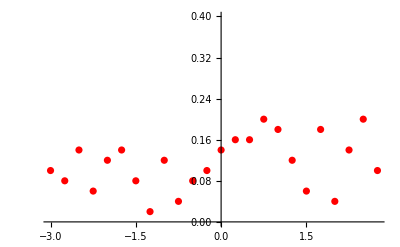

```mathematica
bprior=ListPlot[Table[{priorrange[[i]],BinCounts[priordata,{-3,3,0.25}][[i]]/200*4},{i,0,24}],PlotRange->{0,0.4},PlotStyle->Red]
```

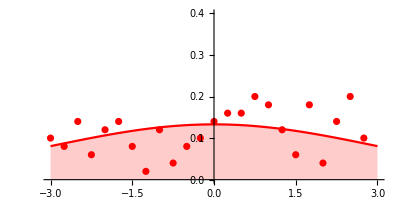

```mathematica
Show[priordist,bprior, AspectRatio->1/2]
```

```mathematica
p=RandomVariate[NormalDistribution[1,1],10000];
```

```mathematica
q=RandomVariate[NormalDistribution[0.5,1.25],10000];
```

```mathematica
barrange=Range[-3,3,0.1];
```

```mathematica
bp=BarChart[BinCounts[p,{-3,3,0.1}]/10000/0.1, ChartStyle->{Directive[Blue,Opacity[0.5], EdgeForm[]]}];
```

```mathematica
bq=BarChart[BinCounts[q,{-3,3,0.1}]/10000/0.1,ChartStyle->{Directive[Purple,Opacity[0.2], EdgeForm[]]}];
```

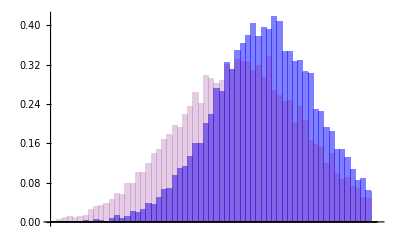

```mathematica
Show[bp,bq]
```

```mathematica
bpl=ListPlot[Table[{barrange[[i]],BinCounts[p,{-3,3,0.1}][[i]]/10000/0.1},{i,60}],PlotStyle->Blue,Filling->Axis];
```

```mathematica
bql=ListPlot[Table[{barrange[[i]],BinCounts[q,{-3,3,0.1}][[i]]/10000/0.1},{i,60}],PlotStyle->{Purple,Opacity[0.4]},Filling->Axis];
```

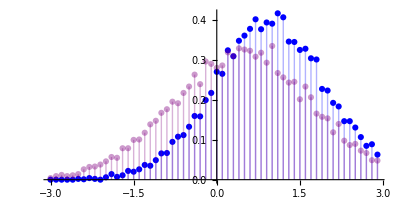

```mathematica
Show[bpl,bql,AspectRatio->1/2]
```

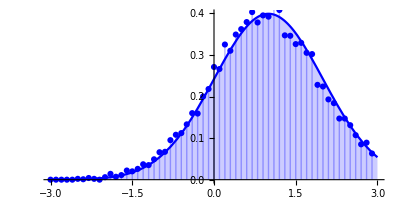

```mathematica
Show[pdist,bpl,AspectRatio->1/2]
```

```mathematica
mcmcdata=RandomVariate[NormalDistribution[1,1],2000];
```

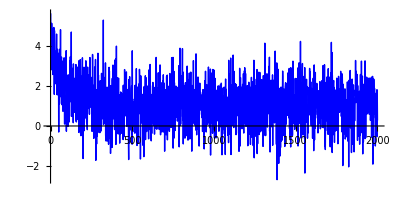

```mathematica
ListLinePlot[Table[{i,Exp[1-i/100]+mcmcdata[[i]]},{i,2000}],PlotStyle->{Blue,Thin}, AspectRatio->1/2]
```